```mathematica
coefs={0.2770153415322121,1.1081373379120663,-0.0467877603240845,-0.8003226905064302,0.0098227502646689,0.5357830054737038,0.0865435588286316,-0.2909212617013319,-0.0573566509014459,0.0482234648139953,-0.0638874791003932,0.0628162260607810,-0.0125002182844017,0.0313459776986805,-0.0036927614912847,0.0137221051007593};
```

```mathematica
F[x_]:=Sin[x]+LogisticSigmoid[x]
min=-2Pi;
max=2Pi;
```

```mathematica
FourierApprox[coefs_][x_]:=Sum[coefs[[i+1]]*Sin[i*x], {i, 0,Length[coefs]-1}]
TaylorApprox[coefs_][x_]:=Sum[coefs[[i+1]]*x^i/Factorial[i], {i, 0, Length[coefs]-1}]
IntegralLoss[f_]:=NIntegrate[(F[x]-f[f[x]])^2, {x, min, max}]
```

```mathematica
approx=TaylorApprox[coefs];
```

```mathematica
IntegralLoss[approx]
```

0.433118

```mathematica
Iconize[approx[x]]
```

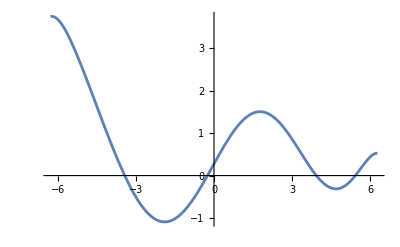

```mathematica
Plot[ approx[x], {x, min, max}]
```

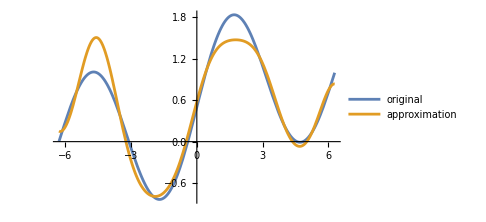

```mathematica
Plot[{F[x], approx[approx[x]]}, {x, min, max}, PlotLegends->{"original", "approximation"}, ImageSize->Medium]
```

```mathematica
Iconize[%]
```

```mathematica
approx[x]
```

0.277015+1.10814 x-0.0233939 x^2-0.133387 x^3+0.000409281 x^4+0.00446486 x^5+0.000120199 x^6-0.0000577225 x^7-1.42254×10^-6 x^8+1.32891×10^-7 x^9-1.76057×10^-8 x^10+1.57368×10^-9 x^11-2.60964×10^-11 x^12+5.03386×10^-12 x^13-4.23587×10^-14 x^14+1.04935×10^-14 x^15

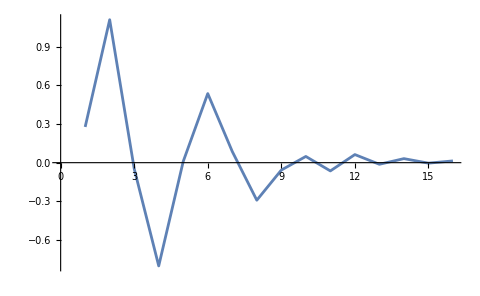

```mathematica
ListLinePlot[coefs]
```